```mathematica
Manipulate[
Module[{x,y},

x=Sin[t]*Sin[t/2]^m+0.5;
y=Cos[t]+1;

ParametricPlot[{x,y},{t,0,6},AxesOrigin->{0,0}]
],
Control[{{m,5,""},0,7,1,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{x,y,z,p1,p2},

x=Sin[t]*Sin[t/2]^n+0.5;
y=Sin[t]*Sin[t/2]^n+0.5;
z=Cos[t]+1;

p1=ParametricPlot3D[{x,y,z},{t,0,6},AxesOrigin->{0,0}];
p2=RevolutionPlot3D[z,{t,0,6},AxesOrigin->{0,0}];

Grid[{{Show[p1],Show[p2]}}]
],
Control[{{n,5,""},0,7,1,Appearance->"Labeled"}]
]
```

```mathematica
Module[{fx,fy,fz,p1,p2},
fx=(1-Cos[θ])*Sin[θ]*Cos[ϕ];
fy=(1-Cos[θ])*Sin[θ]*Sin[ϕ];
fz=2*Cos[θ];

(*p1=ParametricPlot3D[{{fx,fy,fz},0.5*{fx,fy,fz}},{θ,0,2 π},{ϕ,0,2 π},
PlotRange->{{-1.5,1.5},{0,2}},
ImageSize->400,
ViewPoint->Front,
Mesh->None,
PlotStyle->{Opacity[0.35,Orange],Red},
Lighting->{{"Ambient", White}}];*)

p2=Show[
ParametricPlot3D[Table[{fx+3*n,fy,fz},{n,0,5}],{θ,0,2 π},{ϕ,0,2 π},
PlotRange->{{-1.5,Automatic},{0,2}},
PlotStyle->Orange,
Mesh->None],
ParametricPlot3D[Table[{0.5*fx+3*n,0.5*fy,0.5*fz-1},{n,0,5}],{θ,0,2 π},{ϕ,0,2 π},
PlotStyle->Red,
Mesh->None],
ImageSize->400,
ViewPoint->Front];

(*Grid[{{Show[p1],Spacer[10],Show[p2]}}]*)
Show[p2]
]
```

-Graphics3D-

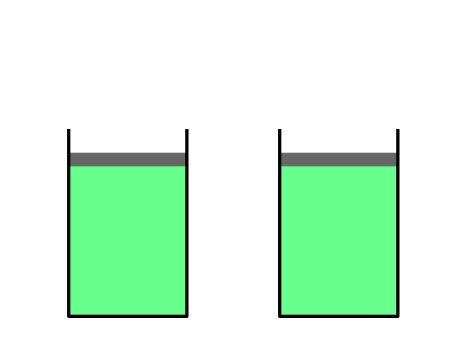

```mathematica
Manipulate[

Graphics[{
{Opacity[0.7,RGBColor[0.16,1.,0.36]],Rectangle[{0,0},{0.7,0.9}],Rectangle[{1.25,0},{1.95,0.9}]},
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,0.9},{0.7,0.975}],Rectangle[{1.25,0.9},{1.95,0.975}]},
{Thickness[0.005],Line[{{0,1.12},{0,0},{0.7,0},{0.7,1.12}}],Line[{{1.25,1.12},{1.25,0},{1.95,0},{1.95,1.12}}]}

},ImageSize->{475,350},PlotRange->{{-0.15,2.15},{-0.01,1.7}}],

Control[{{cs,True,""},{True,False}}]]
```